# Order parameters and χ4 for p0=3.75

## angular averaged translational order parameter

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/localTest/2DmeltingPhase/N4096/";
```

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.016 ,0.01, 0.008 ,0.0063 ,0.005 ,0.00385, 0.0031, 0.0028 ,0.0025, 0.0022 ,0.002};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000}

```mathematica
orientation=Table[Import[StringJoin[saveFolder,"orientationReIm_N4096_p3.750_T",Tstring[[T]],"_0.nc"],"Data"][[1]],{T,Length[Tlist]}];
```

```mathematica
translation=Table[Import[StringJoin[saveFolder,"timeTranslation_N4096_p3.750_T",Tstring[[T]],"_0.nc"],"Data"][[2]],{T,Length[Tlist]}];
```

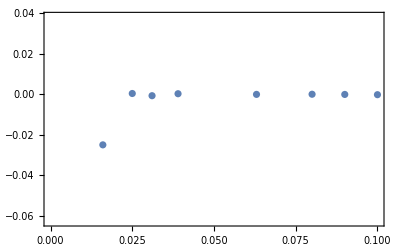

```mathematica
ListPlot[Table[{Tlist[[T]],Mean[Normal[orientation[[T]]]]},{T,Length[Tlist]}]]
```

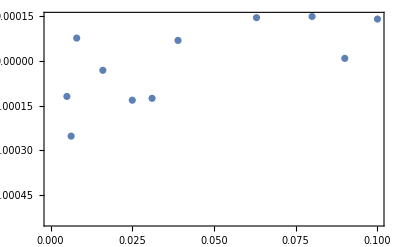

```mathematica
ListPlot[Table[{Tlist[[T]],Mean[Normal[translation[[T]]]]},{T,Length[Tlist]}]]
```

```mathematica
4096*Variance[Normal[orientation[[15]]]]
```

0.649575

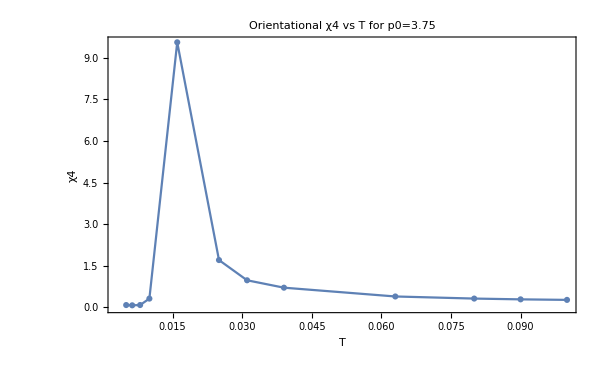

```mathematica
orientationchi4Plot=ListPlot[Table[{Tlist[[T]],4096*Variance[Normal[orientation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotRange->All,FrameLabel->{"T","χ4"},ImageSize->600,PlotLabel->"Orientational χ4 vs T for p0=3.75",PlotMarkers->Automatic]
```

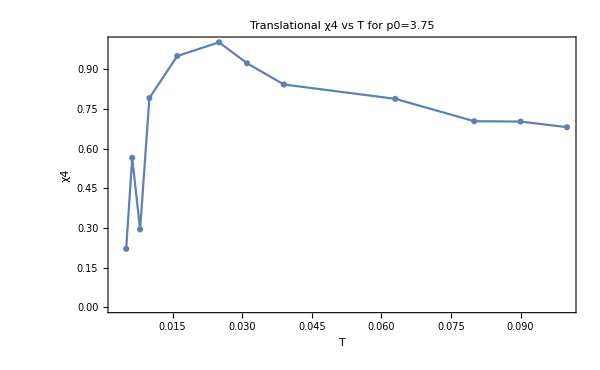

```mathematica
translationalChi4Plot=ListPlot[Table[{Tlist[[T]],4096*Variance[Normal[translation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotRange->All,FrameLabel->{"T","χ4"},ImageSize->600,PlotLabel->"Translational χ4 vs T for p0=3.75",PlotMarkers->Automatic]
```

## k is (2Pi,0)

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/localTest/2DmeltingPhase/N4096/p375/";
```

```mathematica
Tlist={0.10 ,0.09 ,0.08 ,0.063 ,0.039, 0.03105 ,0.025, 0.016 ,0.01 ,0.008, 0.0063, 0.005};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.10000000,0.09000000,0.08000000,0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000}

```mathematica
orientation=Table[Import[StringJoin[saveFolder,"orientationReIm_N4096_p3.750_T",Tstring[[T]],"_0.nc"],"Data"],{T,Length[Tlist]}];
```

```mathematica
translation=Table[Import[StringJoin[saveFolder,"otranslationReIm_N4096_p3.750_T",Tstring[[T]],"_0.nc"],"Data"],{T,Length[Tlist]}];
```

```mathematica
absOrientation=Table[Table[Sqrt[orientation[[T,1,i]]^2+orientation[[T,2,i]]^2],{i,Length[orientation[[T,1]]]}],{T,Length[Tlist]}];
```

```mathematica
absTranslation=Table[Table[Sqrt[translation[[T,1,i]]^2+translation[[T,2,i]]^2],{i,Length[orientation[[T,1]]]}],{T,Length[Tlist]}];
```

```mathematica
absOrientation[[1]]
```

{}

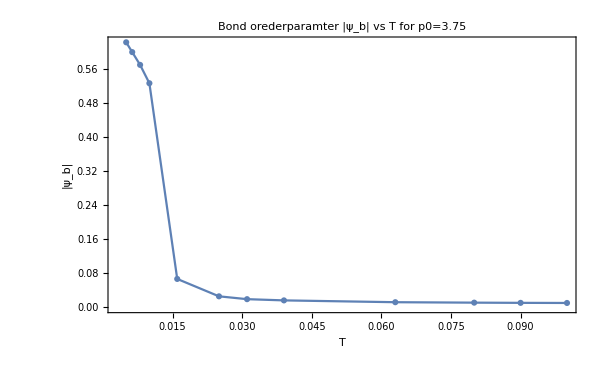

```mathematica
bondOrderPlot=ListPlot[Table[{Tlist[[T]],Mean[absOrientation[[T]]]},{T,Length[Tlist]}],PlotRange->All,FrameLabel->{"T","|ψ_b|"},ImageSize->600,PlotLabel->"Bond orederparamter |ψ_b| vs T for p0=3.75",PlotMarkers->Automatic,Joined->True]
```

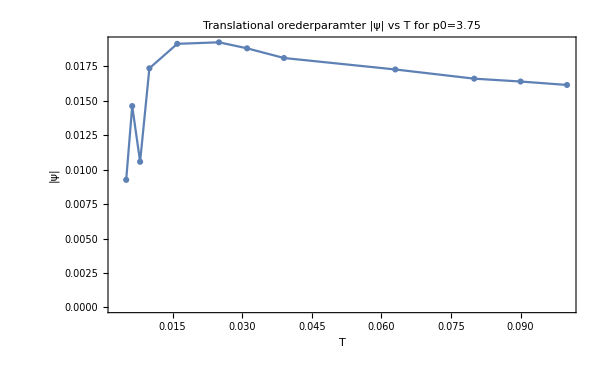

```mathematica
transOrderPlot=ListPlot[Table[{Tlist[[T]],Mean[absTranslation[[T]]]},{T,Length[Tlist]}],PlotRange->All,FrameLabel->{"T","|ψ|"},ImageSize->600,PlotLabel->"Translational orederparamter |ψ| vs T for p0=3.75",PlotMarkers->Automatic,Joined->True]
```

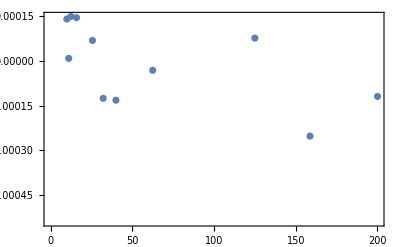

```mathematica
ListPlot[Table[{1/Tlist[[T]],Mean[Normal[translation[[T]]]]},{T,Length[Tlist]}]]
```

```mathematica
4096*Variance[Normal[orientation[[15]]]]
```

0.649575

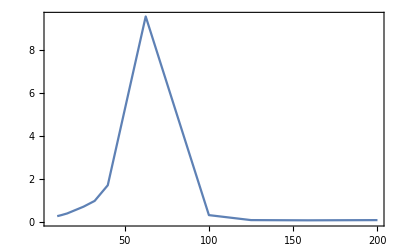

```mathematica
ListPlot[Table[{1/Tlist[[T]],4096*Variance[Normal[orientation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotRange->All]
```

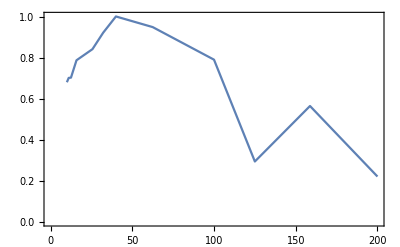

```mathematica
ListPlot[Table[{1/Tlist[[T]],4096*Variance[Normal[translation[[T]]]]},{T,Length[Tlist]}],Joined->True]
```

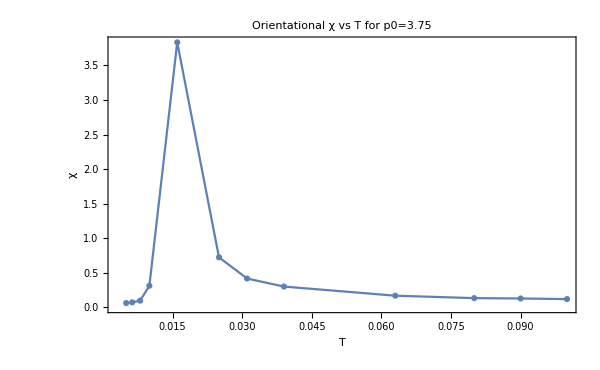

```mathematica
orientationchi4Plot=ListPlot[Table[{Tlist[[T]],4096*Variance[Normal[absOrientation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotRange->All,FrameLabel->{"T","χ"},ImageSize->600,PlotLabel->"Orientational χ vs T for p0=3.75",PlotMarkers->Automatic]
```

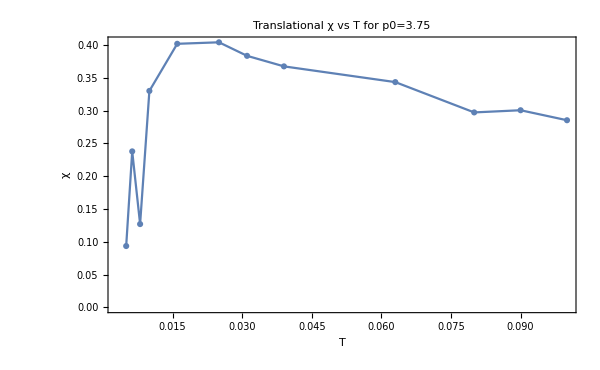

```mathematica
translationalChi4Plot=ListPlot[Table[{Tlist[[T]],4096*Variance[Normal[absTranslation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotRange->All,FrameLabel->{"T","χ"},ImageSize->600,PlotLabel->"Translational χ vs T for p0=3.75",PlotMarkers->Automatic]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/orientationalchi4_p375.jpeg",orientationchi4Plot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tranlationalchi4_p375.jpeg",translationalChi4Plot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/bondorderParameter_p375.jpeg",bondOrderPlot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/transorderParameter_p375.jpeg",transOrderPlot,ImageResolution->600];
```